```mathematica
(*  Guy F. Mongelli                               ChE 400
   Prof. Clark                                   9/26/2010     *)
```

```mathematica
(*  Assignment #4 *)
```

```mathematica
(* Problem #1   *)
```

```mathematica
(*  Important resource for fourier sine and cosine series

http://www.sosmath.com/fourier/fourier2/fourier2.html   *)
```

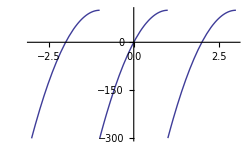

```mathematica
L=1;
T0=100 (* degrees C *);
a=2;
b=1;
fbas[x_]:=4*T0*(x/a)(1-x/a);
f[x_]:=fbas[Mod[x,2×L,-L]];
graphoneF=Plot[f[x],{x,-3,3}]
```

```mathematica
aF[n_]=Simplify[2/L∫_-L^L f[x]Cos[(n π x)/L]ⅆx,n∈Integers]
```

(4 (-1)^n)/(n^2 π^2)

```mathematica
bF[n_]=Simplify[1/L∫_-L^L f[x]Sin[(n π x)/L]ⅆx,n∈Integers]
```

(2 (-1)^n (-6+n^2 π^2))/(n^3 π^3)

```mathematica
coeffsF=Table[{aF[i],bF[i]},{i,1,20}];
TableForm[coeffsF]
```

-4/π^2 | -(2 (-6+π^2))/π^3
1/π^2 | (-6+4 π^2)/(4 π^3)
-4/(9 π^2) | -(2 (-6+9 π^2))/(27 π^3)
1/(4 π^2) | (-6+16 π^2)/(32 π^3)
-4/(25 π^2) | -(2 (-6+25 π^2))/(125 π^3)
1/(9 π^2) | (-6+36 π^2)/(108 π^3)
-4/(49 π^2) | -(2 (-6+49 π^2))/(343 π^3)
1/(16 π^2) | (-6+64 π^2)/(256 π^3)
-4/(81 π^2) | -(2 (-6+81 π^2))/(729 π^3)
1/(25 π^2) | (-6+100 π^2)/(500 π^3)
-4/(121 π^2) | -(2 (-6+121 π^2))/(1331 π^3)
1/(36 π^2) | (-6+144 π^2)/(864 π^3)
-4/(169 π^2) | -(2 (-6+169 π^2))/(2197 π^3)
1/(49 π^2) | (-6+196 π^2)/(1372 π^3)
-4/(225 π^2) | -(2 (-6+225 π^2))/(3375 π^3)
1/(64 π^2) | (-6+256 π^2)/(2048 π^3)
-4/(289 π^2) | -(2 (-6+289 π^2))/(4913 π^3)
1/(81 π^2) | (-6+324 π^2)/(2916 π^3)
-4/(361 π^2) | -(2 (-6+361 π^2))/(6859 π^3)
1/(100 π^2) | (-6+400 π^2)/(4000 π^3)

```mathematica
Fs[k_,x_]:=coeffsF[[k,2]]*Sin[k*Pi*x/L]+coeffsF[[k,1]]*Cos[k*Pi*x/L]
```

```mathematica
(* Defining a Fourier Sine Series, Fourier Cosine Series, and Full Fourier Series for f   *)
```

```mathematica
Fs[5,x]
```

-(4 Cos[5 π x])/(25 π^2)-(2 (-6+25 π^2) Sin[5 π x])/(125 π^3)

```mathematica
fourierF[n_,x_]:=aF[0]+∑_(k=1)^n Fs[k,x]
```

```mathematica
fourierF[5,x]
```

4/3-(4 Cos[π x])/π^2+Cos[2 π x]/π^2-(4 Cos[3 π x])/(9 π^2)+Cos[4 π x]/(4 π^2)-(4 Cos[5 π x])/(25 π^2)-(2 (-6+π^2) Sin[π x])/π^3+((-6+4 π^2) Sin[2 π x])/(4 π^3)-(2 (-6+9 π^2) Sin[3 π x])/(27 π^3)+((-6+16 π^2) Sin[4 π x])/(32 π^3)-(2 (-6+25 π^2) Sin[5 π x])/(125 π^3)

```mathematica
N[fourierF[5,x],1]
```

1.-0.4 Cos[3. x]+0.1 Cos[6. x]-0.05 Cos[9. x]+0.03 Cos[10. x]-0.02 Cos[20. x]-0.2 Sin[3. x]+0.3 Sin[6. x]-0.2 Sin[9. x]+0.2 Sin[10. x]-0.1 Sin[20. x]

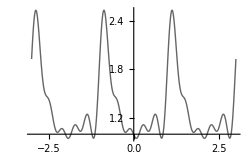

```mathematica
graphtwoF=Plot[fourierF[5,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

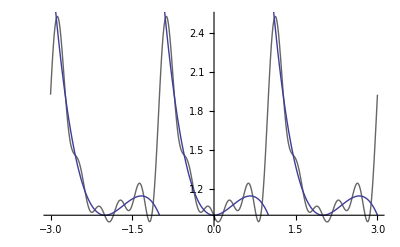

```mathematica
bothtwoF=Show[graphtwoF,graphoneF]
```

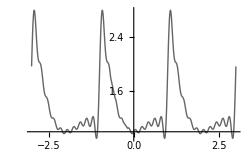

```mathematica
graphthreeF=Plot[fourierF[10,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

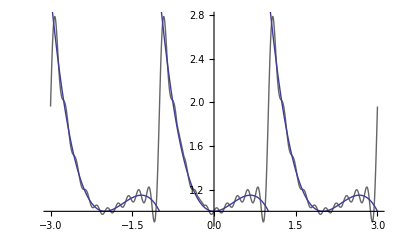

```mathematica
boththreeF=Show[graphthreeF,graphoneF]
```

```mathematica
graphsixF=Plot[fourierF[20,x],{x,-3,3},PlotStyle->GrayLevel[0.4]];
```

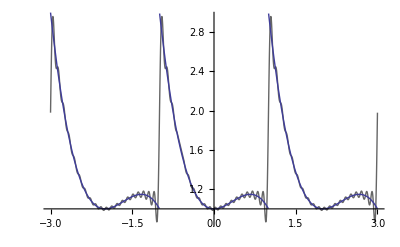

```mathematica
bothsixF=Show[graphsixF,graphoneF]
```

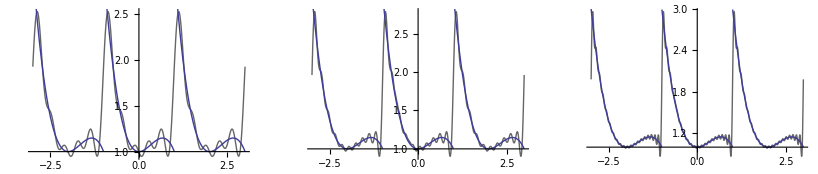

```mathematica
Show[GraphicsRow[{bothtwoF,boththreeF,bothsixF}]]
```

```mathematica
(* Part B *)
```

```mathematica
(* Now consider the Fourier Sine Series for F.  The Fourier Sine Series is the periodic extension of the odd extension of x. *)
```

```mathematica
fbasod[x_]:=If[(x≥0),fbas[x],-fbas[-x]];
fod[x_]:=fbasod[Mod[x,2*L,-L]];
```

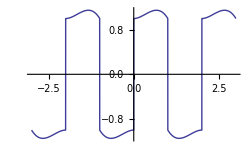

```mathematica
graphoneFSine=Plot[fod[x],{x,-3,3}]
```

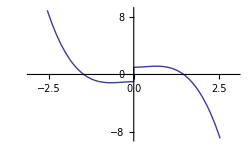

```mathematica
Plot[fbasod[x],{x,-3,3}]
```

```mathematica
(* The odd extended function is discontinuous every 2L period.  Therefore, the periodic extension of the odd extension will have foruier coefficients that drop of as 1/n.  *)
```

```mathematica
aFSine[0]=1/(2 L)∫_-L^L fod[x]ⅆx
```

0

```mathematica
aFSine[n_]=Simplify[1/L∫_-L^L fod[x]Cos[(n π x)/L]ⅆx,n∈Integers]
```

0

```mathematica
bFSine[n_]=Simplify[1/L∫_-L^L fod[x]Sin[(n π x)/L]ⅆx,n∈Integers]
```

-(2 (2+4 (-1)^n+(-1+(-1)^n) n^2 π^2))/(n^3 π^3)

```mathematica
coeffsFSine=Table[{aFSine[i],bFSine[i]},{i,1,20}];
TableForm[coeffsFSine]
```

0 | -(2 (-2-2 π^2))/π^3
0 | -3/(2 π^3)
0 | -(2 (-2-18 π^2))/(27 π^3)
0 | -3/(16 π^3)
0 | -(2 (-2-50 π^2))/(125 π^3)
0 | -1/(18 π^3)
0 | -(2 (-2-98 π^2))/(343 π^3)
0 | -3/(128 π^3)
0 | -(2 (-2-162 π^2))/(729 π^3)
0 | -3/(250 π^3)
0 | -(2 (-2-242 π^2))/(1331 π^3)
0 | -1/(144 π^3)
0 | -(2 (-2-338 π^2))/(2197 π^3)
0 | -3/(686 π^3)
0 | -(2 (-2-450 π^2))/(3375 π^3)
0 | -3/(1024 π^3)
0 | -(2 (-2-578 π^2))/(4913 π^3)
0 | -1/(486 π^3)
0 | -(2 (-2-722 π^2))/(6859 π^3)
0 | -3/(2000 π^3)

```mathematica
FsSine[k_,x_]:=coeffsFSine[[k,1]]*Sin[k*Pi*x/L]+coeffsFSine[[k,1]]*Cos[k*Pi*x/L]
```

```mathematica
fourierFSine[n_,x_]:=aF[0]+∑_(k=1)^n Fs[k,x]
```

```mathematica
fourierFSine[5,x]
```

4/3-(4 Cos[π x])/π^2+Cos[2 π x]/π^2-(4 Cos[3 π x])/(9 π^2)+Cos[4 π x]/(4 π^2)-(4 Cos[5 π x])/(25 π^2)-(2 (-6+π^2) Sin[π x])/π^3+((-6+4 π^2) Sin[2 π x])/(4 π^3)-(2 (-6+9 π^2) Sin[3 π x])/(27 π^3)+((-6+16 π^2) Sin[4 π x])/(32 π^3)-(2 (-6+25 π^2) Sin[5 π x])/(125 π^3)

```mathematica
graphtwoFSine=Plot[fourierFSine[5,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

-Graphics-

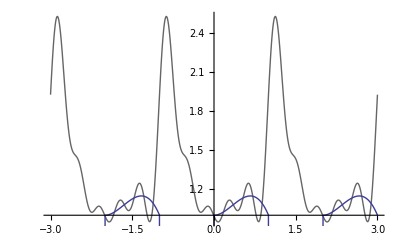

```mathematica
bothtwoFSine=Show[graphtwoFSine,graphoneFSine]
```

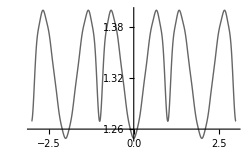

```mathematica
graphthreeFSine=Plot[fourierFSine[10,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

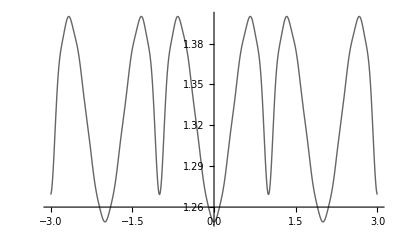

```mathematica
boththreeFSine=Show[graphthreeFSine,graphoneFSine]
```

```mathematica
graphsixFSine=Plot[fourierF[20,x],{x,-3,3},PlotStyle->GrayLevel[0.4]];
```

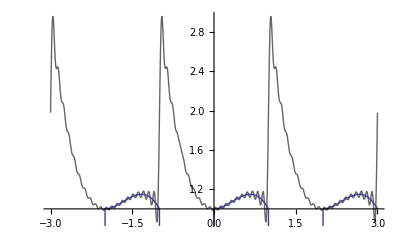

```mathematica
bothsixFSine=Show[graphsixFSine,graphoneFSine]
```

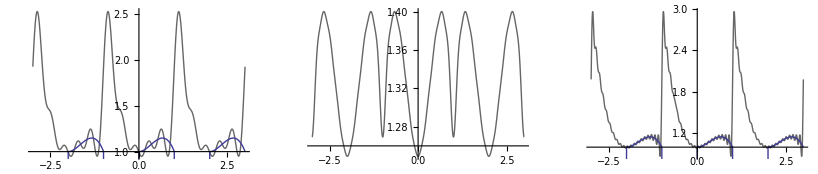

```mathematica
Show[GraphicsRow[{bothtwoFSine,boththreeFSine,bothsixFSine}]]
```

```mathematica
(* Part C   *)
```

```mathematica
(* The Fourier Cosine series is the periodic extension of the odd extension of x.  *)
```

```mathematica
fbasev[x_]:=If[(x≥0),fbas[x],fbas[-x]];
fev[x_]:=fbasev[Mod[x,2*L,-L]];
```

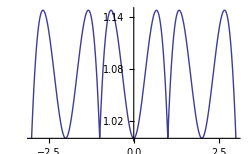

```mathematica
graphoneFCos=Plot[fev[x],{x,-3,3}]
```

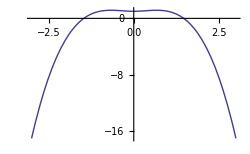

```mathematica
Plot[fbasev[x],{x,-3,3}]
```

```mathematica
(* The even extended function is discontinuous once per 2L period, therefore the full fourier series will converge as 1/n  (the lowest power of n in the denominator of any term)  *)
```

```mathematica
aFCos[0]=1/(2 L)∫_-L^L fev[x]ⅆx
```

13/12

```mathematica
aFCos[n_]=Simplify[1/L∫_-L^L fev[x]Cos[(n π x)/L]ⅆx,n∈Integers]
```

-(2 (6-6 (-1)^n+(-1)^n n^2 π^2))/(n^4 π^4)

```mathematica
bFCos[n_]=Simplify[1/L∫_-L^L fev[x]Sin[(n π x)/L]ⅆx,n∈Integers]
```

0

```mathematica
coeffsFCos=Table[{aFCos[i],bFCos[i]},{i,1,20}];
TableForm[coeffsF]
```

-(2 (12-π^2))/π^4 | 0
-1/(2 π^2) | 0
-(2 (12-9 π^2))/(81 π^4) | 0
-1/(8 π^2) | 0
-(2 (12-25 π^2))/(625 π^4) | 0
-1/(18 π^2) | 0
-(2 (12-49 π^2))/(2401 π^4) | 0
-1/(32 π^2) | 0
-(2 (12-81 π^2))/(6561 π^4) | 0
-1/(50 π^2) | 0
-(2 (12-121 π^2))/(14641 π^4) | 0
-1/(72 π^2) | 0
-(2 (12-169 π^2))/(28561 π^4) | 0
-1/(98 π^2) | 0
-(2 (12-225 π^2))/(50625 π^4) | 0
-1/(128 π^2) | 0
-(2 (12-289 π^2))/(83521 π^4) | 0
-1/(162 π^2) | 0
-(2 (12-361 π^2))/(130321 π^4) | 0
-1/(200 π^2) | 0

```mathematica
FsCos[k_,x_]:=coeffsFCos[[k,2]]*Sin[k*Pi*x/L]+coeffsFCos[[k,1]]*Cos[k*Pi*x/L]
```

```mathematica
(* Defining a Fourier Cosine for an evenly extended f   *)
```

```mathematica
FsCos[5,x]
```

-(2 (12-25 π^2) Cos[5 π x])/(625 π^4)

```mathematica
fourierFCos[n_,x_]:=aF[0]+∑_(k=1)^n Fs[k,x]
```

```mathematica
fourierFCos[5,x]
```

4/3-(2 (12-π^2) Cos[π x])/π^4-Cos[2 π x]/(2 π^2)-(2 (12-9 π^2) Cos[3 π x])/(81 π^4)-Cos[4 π x]/(8 π^2)-(2 (12-25 π^2) Cos[5 π x])/(625 π^4)

```mathematica
N[fourierFCos[5,x],1]
```

1.-0.04 Cos[3. x]-0.05 Cos[6. x]+0.02 Cos[9. x]-0.01 Cos[10. x]+0.008 Cos[20. x]

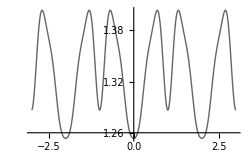

```mathematica
graphtwoFCos=Plot[fourierFCos[5,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

```mathematica
bothtwoFCos=Show[graphtwoFCos,graphoneFCos]
```

-Graphics-

```mathematica
graphthreeFCos=Plot[fourierFCos[10,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

-Graphics-

```mathematica
boththreeFCos=Show[graphthreeFCos,graphoneFCos]
```

-Graphics-

```mathematica
graphsixFCos=Plot[fourierFCos[20,x],{x,-3,3},PlotStyle->GrayLevel[0.4]];
```

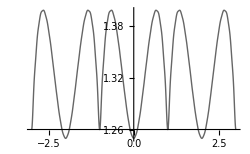

```mathematica
bothsixFCos=Show[graphsixFCos,graphoneFCos]
```

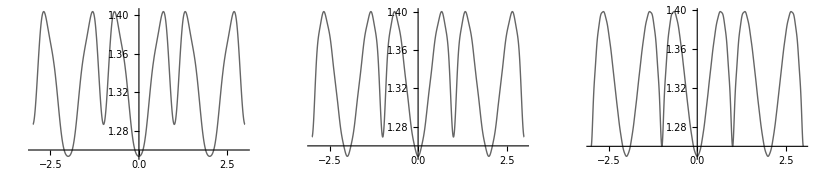

```mathematica
Show[GraphicsRow[{bothtwoFCos,boththreeFCos,bothsixFCos}]]
```

```mathematica
(* Problem #2  *)
```

```mathematica
(* Problem #3  *)
```

```mathematica
Clear[L,y0,v0,f,g,c,y,v]
```

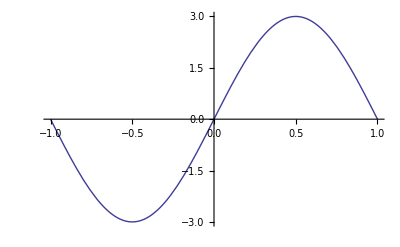

```mathematica
c=1;
L=1;
y0=3;
v0=4;
f[x_]:=y0*Sin[(π*x)/L];
graphoneF=Plot[f[x],{x,-L,L}]
```

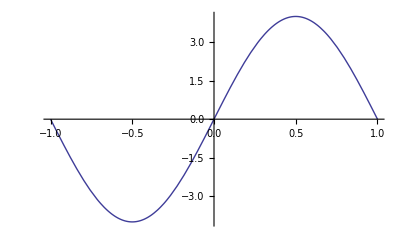

```mathematica
g[x_]:=v0*Sin[(π*x)/L];
graphoneG=Plot[g[x],{x,-L,L}]
```

```mathematica
w[n_]:=(n*π*c)/L
```

```mathematica
(* Given the initial conditions, all of the fourier coefficients will be zero except for n=1  *)
```

```mathematica
aF[n_]=Simplify[2/L∫_0^L f[x]Sin[(  π x)/L]ⅆx,n∈Integers]
```

3

```mathematica
bF[n_]=Simplify[2/(w[n]*L)∫_-L^L g[x]Sin[( π x)/L]ⅆx,n∈Integers]
```

8/(n π)

```mathematica
coeffsF=Table[{aF[i],bF[i],w[i]},{i,1,20}];
TableForm[coeffsF]
```

3 | 8/π | π
3 | 4/π | 2 π
3 | 8/(3 π) | 3 π
3 | 2/π | 4 π
3 | 8/(5 π) | 5 π
3 | 4/(3 π) | 6 π
3 | 8/(7 π) | 7 π
3 | 1/π | 8 π
3 | 8/(9 π) | 9 π
3 | 4/(5 π) | 10 π
3 | 8/(11 π) | 11 π
3 | 2/(3 π) | 12 π
3 | 8/(13 π) | 13 π
3 | 4/(7 π) | 14 π
3 | 8/(15 π) | 15 π
3 | 1/(2 π) | 16 π
3 | 8/(17 π) | 17 π
3 | 4/(9 π) | 18 π
3 | 8/(19 π) | 19 π
3 | 2/(5 π) | 20 π

```mathematica
Fs[k_,x_,t_]:={aF[n]*Cos[w[n]*t]+bF[n]*Sin[w[n]*t]}*Sin[(k π x)/L]
```

```mathematica
(* Defining a Fourier Sine Series, Fourier Cosine Series, and Full Fourier Series for f   *)
```

```mathematica
Fs[1,x,t]
```

{(3 Cos[n π t]+(8 Sin[n π t])/(n π)) Sin[π x]}

```mathematica
fourierF[n_,x_,t_]:=∑_(k=1)^n Fs[k,x,t]
```

```mathematica
fourierF[5,x,t]
```

{(3 Cos[n π t]+(8 Sin[n π t])/(n π)) Sin[π x]+(3 Cos[n π t]+(8 Sin[n π t])/(n π)) Sin[2 π x]+(3 Cos[n π t]+(8 Sin[n π t])/(n π)) Sin[3 π x]+(3 Cos[n π t]+(8 Sin[n π t])/(n π)) Sin[4 π x]+(3 Cos[n π t]+(8 Sin[n π t])/(n π)) Sin[5 π x]}

```mathematica
N[fourierF[5,x,t],1]
```

{(3. Cos[3. n t]+(3. Sin[3. n t])/n) Sin[3. x]+(3. Cos[3. n t]+(3. Sin[3. n t])/n) Sin[6. x]+(3. Cos[3. n t]+(3. Sin[3. n t])/n) Sin[9. x]+(3. Cos[3. n t]+(3. Sin[3. n t])/n) Sin[10. x]+(3. Cos[3. n t]+(3. Sin[3. n t])/n) Sin[20. x]}

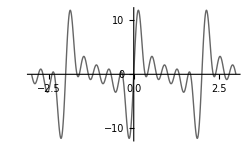

```mathematica
graphtwoF=Plot[fourierF[5,x,0],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

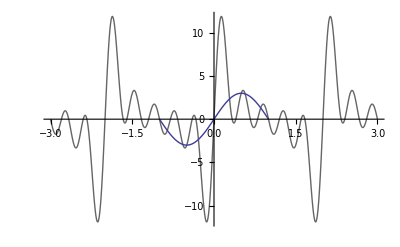

```mathematica
bothtwoF=Show[graphtwoF,graphoneF]
```

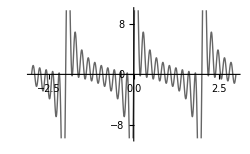

```mathematica
graphthreeF=Plot[fourierF[10,x,0],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

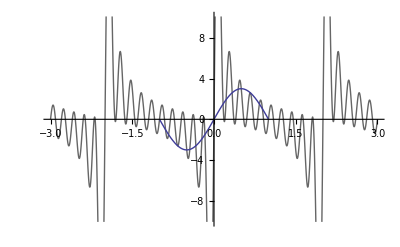

```mathematica
boththreeF=Show[graphthreeF,graphoneF]
```

```mathematica
graphsixF=Plot[fourierF[20,x,0],{x,-3,3},PlotStyle->GrayLevel[0.4]];
```

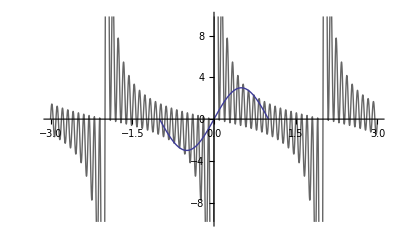

```mathematica
bothsixF=Show[graphsixF,graphoneF]
```

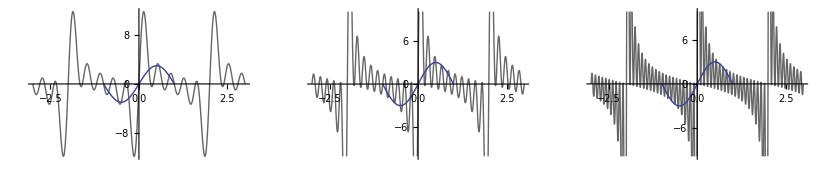

```mathematica
Show[GraphicsRow[{bothtwoF,boththreeF,bothsixF}]]
```

```mathematica
(* Challenge Problem  *)
```